# Analysis with asymmetric host and symbiont dispersal rates

## Setup:

Clear kernel of unwanted junk!

```mathematica
(*Quit[]*)
```

Setup dynamical expressions. First, I start by determining the average payoff of each host and symbiont phenotype in each environment:

```mathematica
ΔW1S1=s1* ΔHms-(1-s1) ΔHgh;
ΔW2S2=s2* ΔHgh-(1-s2) ΔHms;
ΔV1H1=h1* ΔSmh-(1-h1) ΔSgs;
ΔV2H2=h2* ΔSgs-(1-h2) ΔSmh;
```

Modified replicator equation to give the frequency of each strategist in each patch and allow dispersal between the patches:

```mathematica
H1d=h1*(1-h1)*(ΔW1S1)+dh*h2-dh*h1;
H2d= h2*(1-h2)*(ΔW2S2)-dh*h2+dh*h1;
S1d=s1*(1-s1)*(ΔV1H1)+ds*s2-ds*s1;
S2d=s2*(1-s2)*(ΔV2H2)-ds*s2+ds*s1;
```

## Boundary Equilibria:

### First I’ll try out some boundary equilibria:

What if we just tried out all the boundaries and checked out what happens?

```mathematica
J=Simplify[{
{D[H1d, h1],D[H2d,h1],D[S1d,h1],D[S2d,h1]},{D[H1d, h2],D[H2d,h2],D[S1d,h2],D[S2d,h2]},{D[H1d, s1],D[H2d,s1],D[S1d,s1],D[S2d,s1]},{D[H1d, s2],D[H2d,s2],D[S1d,s2],D[S2d,s2]}}];
candidates=Tuples[{0,1},4];(*can also plug in candidates from no dispersal case to get same results. *)
(*Evaluate equations at candidates from no dispersal case and return those that are equilibria. *)
equilibrialist={};
Do[{eval={H1d,H2d,S1d,S2d}/. {h1->candidates[[i,1]],h2->1candidates[[i,2]],s1->candidates[[i,3]], s2->candidates[[i,4]]},If[eval=={0,0,0,0},AppendTo[equilibrialist,candidates[[i]]]]}
,{i,1,Length[candidates]}]
equilibrialist
```

{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,1,1}}

(h1e1,h1e2,s1e1,s1e2)
So there are only two sets of boundary equilibria. One where one genotype fixes everywhere, and another when genotypes and environments mismatch.

Let’s evaluate the Jacobian for the mismatching environment, matching genotype equilibrium:

```mathematica
J/.{h1-> 0,s1-> 0,h2-> 0,s2-> 0}//MatrixForm
J/.{h1-> 1,s1-> 1,h2-> 1,s2-> 1}//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-dh-ΔHgh | dh | 0 | 0
dh | -dh-ΔHms | 0 | 0
0 | 0 | -ds-ΔSgs | ds
0 | 0 | ds | -ds-ΔSmh)

(-dh-ΔHms | dh | 0 | 0
dh | -dh-ΔHgh | 0 | 0
0 | 0 | -ds-ΔSmh | ds
0 | 0 | ds | -ds-ΔSgs)

{{-dh-ΔHms,dh},{dh,-dh-ΔHgh}}

{{-ds-ΔSmh,ds},{ds,-ds-ΔSgs}}

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
```

2 ds+ΔSgs+ΔSmh

ds ΔSgs+ds ΔSmh+ΔSgs ΔSmh

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
```

2 dh+ΔHgh+ΔHms

dh ΔHgh+dh ΔHms+ΔHgh ΔHms

```mathematica
J/.{h1-> 0,h2-> 0,s1-> 1,s2-> 1}//MatrixForm
J/.{h1-> 1,h2-> 1,s1-> 0,s2-> 0}//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-dh+ΔHms | dh | 0 | 0
dh | -dh+ΔHgh | 0 | 0
0 | 0 | -ds+ΔSgs | ds
0 | 0 | ds | -ds+ΔSmh)

(-dh+ΔHgh | dh | 0 | 0
dh | -dh+ΔHms | 0 | 0
0 | 0 | -ds+ΔSmh | ds
0 | 0 | ds | -ds+ΔSgs)

{{-dh+ΔHgh,dh},{dh,-dh+ΔHms}}

{{-ds+ΔSmh,ds},{ds,-ds+ΔSgs}}

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
```

2 ds-ΔSgs-ΔSmh

-ds ΔSgs-ds ΔSmh+ΔSgs ΔSmh

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
```

2 dh-ΔHgh-ΔHms

-dh ΔHgh-dh ΔHms+ΔHgh ΔHms

## Approximating Internal Equilibria - both rates of dispersal are small.

```mathematica
assumptionfn[x_] := x/.{ds-> ds*ϵ,dh-> dh*ϵ,h1->h10+ h11*ϵ,h2-> h20+h21*ϵ,s1->s10+s11* ϵ, s2->s20+s21* ϵ};
{H1d,H2d,S1d,S2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{h10,h20,s10,s20}]//FullSimplify
```

{{h10→ΔSgs/(ΔSgs+ΔSmh),h20→0,s10→ΔHgh/(ΔHgh+ΔHms),s20→0},{h10→ΔSgs/(ΔSgs+ΔSmh),h20→1,s10→ΔHgh/(ΔHgh+ΔHms),s20→0},{h10→ΔSgs/(ΔSgs+ΔSmh),h20→0,s10→ΔHgh/(ΔHgh+ΔHms),s20→1},{h10→ΔSgs/(ΔSgs+ΔSmh),h20→1,s10→ΔHgh/(ΔHgh+ΔHms),s20→1},{h10→ΔSgs/(ΔSgs+ΔSmh),h20→ΔSmh/(ΔSgs+ΔSmh),s10→ΔHgh/(ΔHgh+ΔHms),s20→ΔHms/(ΔHgh+ΔHms)},{h10→0,h20→ΔSmh/(ΔSgs+ΔSmh),s10→0,s20→ΔHms/(ΔHgh+ΔHms)},{h10→1,h20→ΔSmh/(ΔSgs+ΔSmh),s10→0,s20→ΔHms/(ΔHgh+ΔHms)},{h10→0,h20→ΔSmh/(ΔSgs+ΔSmh),s10→1,s20→ΔHms/(ΔHgh+ΔHms)},{h10→1,h20→ΔSmh/(ΔSgs+ΔSmh),s10→1,s20→ΔHms/(ΔHgh+ΔHms)},{h10→0,h20→0,s10→0,s20→0},{h10→1,h20→0,s10→0,s20→0},{h10→0,h20→1,s10→0,s20→0},{h10→1,h20→1,s10→0,s20→0},{h10→0,h20→0,s10→1,s20→0},{h10→1,h20→0,s10→1,s20→0},{h10→0,h20→1,s10→1,s20→0},{h10→1,h20→1,s10→1,s20→0},{h10→0,h20→0,s10→0,s20→1},{h10→1,h20→0,s10→0,s20→1},{h10→0,h20→1,s10→0,s20→1},{h10→1,h20→1,s10→0,s20→1},{h10→0,h20→0,s10→1,s20→1},{h10→1,h20→0,s10→1,s20→1},{h10→0,h20→1,s10→1,s20→1},{h10→1,h20→1,s10→1,s20→1}}

```mathematica
ApproximatedEq={};
Do[{sys={H1d,H2d,S1d,S2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h11,h21,s11,s21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]
```

```mathematica
ApproximatedEq;
```

```mathematica
Othorderterms=Table[{JC = J/.{h1->ApproximatedEq[[i,1]],h2-> ApproximatedEq[[i,2]],s1-> ApproximatedEq[[i,3]],s2->ApproximatedEq[[i,4]]}/.{ds->ds ϵ,dh-> dh*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0][[All,1,2]]//Factor,i}
,{i,1,Length[ApproximatedEq]}]
```

{{{-ΔHms,-ΔSmh,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},1},{{ΔHms,ΔSgs,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},2},{{ΔHgh,ΔSmh,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},3},{{-ΔHgh,-ΔSgs,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},4},{{-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},5},{{-ΔHgh,-ΔSgs,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},6},{{ΔHgh,ΔSmh,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},7},{{ΔHms,ΔSgs,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},8},{{-ΔHms,-ΔSmh,-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh))),(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},9},{{-ΔHgh,-ΔHms,-ΔSgs,-ΔSmh},10},{{ΔHgh,-ΔHms,-ΔSmh,ΔSmh},11},{{-ΔHgh,ΔHms,-ΔSgs,ΔSgs},12},{{ΔHgh,ΔHms,ΔSgs,ΔSmh},13},{{-ΔHms,ΔHms,ΔSgs,-ΔSmh},14},{{-ΔHms,-ΔHms,-ΔSmh,-ΔSmh},15},{{ΔHms,ΔHms,ΔSgs,ΔSgs},16},{{-ΔHms,ΔHms,ΔSgs,-ΔSmh},17},{{-ΔHgh,ΔHgh,-ΔSgs,ΔSmh},18},{{ΔHgh,ΔHgh,ΔSmh,ΔSmh},19},{{-ΔHgh,-ΔHgh,-ΔSgs,-ΔSgs},20},{{-ΔHgh,ΔHgh,-ΔSgs,ΔSmh},21},{{ΔHgh,ΔHms,ΔSgs,ΔSmh},22},{{ΔHgh,-ΔHms,-ΔSmh,ΔSmh},23},{{-ΔHgh,ΔHms,-ΔSgs,ΔSgs},24},{{-ΔHgh,-ΔHms,-ΔSgs,-ΔSmh},25}}

```mathematica
unstables={2,3,7,8,11,12,13,14,16,17,18,19,21,22,23,24};(*List of equilibria that must be unstable based on our assumption that ΔHms is always positive*)
filteredeq={};
Do[If[ContainsAny[{i},unstables]==False,AppendTo[filteredeq,ApproximatedEq[[i]]]],{i,1,Length[ApproximatedEq]}]
```

```mathematica
StabilityofEQ[EQ_]:={
EQ//Simplify,
JC = J/.{h1->EQ[[1]],h2-> EQ[[2]],s1-> EQ[[3]],s2->EQ[[4]]}/.{ds->ds ϵ,dh-> dh*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor;
Othorderλs,
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
unsolvedfirstO=Table[{
λ11=a/.Othorderλs[[i]]//Chop//Factor},{i,1,4}];
firsts=firstsp//Flatten;
firsts//Factor//FullSimplify,
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor}
```

### First Internal equilibrium (unstable):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[1]] ];
```

```mathematica
Oth
```

{{λ0→-ΔHms},{λ0→-ΔSmh},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

Never stable unless differences are equal, a marginal case. Oth order terms have opposite signs.

### Second Candidate (unstable or tbd):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[2]] ];
```

```mathematica
eq
```

{(-ds (ΔHgh+ΔHms)+ΔHgh ΔSgs)/(ΔHgh (ΔSgs+ΔSmh)),1-(dh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(ΔHgh ΔSgs-dh (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSgs),1-(ds ΔHms)/((ΔHgh+ΔHms) ΔSgs)}

```mathematica
Oth
```

{{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

Same as above - third and fourth terms are identical save for opposite signs.

### Third Candidate (unstable or tbd):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[3]] ];
```

Part::take: Cannot take positions 1 through 4 in {}.

```mathematica
Oth
```

{{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

the approximated first and second eigenvalues are opposite signs of the third and fourth.

### Fourth Candidate (unstable or tbd):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[4]] ];
```

```mathematica
eq
```

{(dh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(ds (ΔHgh+ΔHms)+ΔHgh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(ds ΔHms)/((ΔHgh+ΔHms) ΔSgs),(ΔHms ΔSgs+dh (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSgs)}

```mathematica
Oth
```

{{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

### Fifth Candidate (unstable or tbd):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[5]] ];
```

```mathematica
eq
```

{1-(dh ΔSgs)/(ΔHms (ΔSgs+ΔSmh)),(-ds (ΔHgh+ΔHms)+ΔHms ΔSmh)/(ΔHms (ΔSgs+ΔSmh)),1-(ds ΔHgh)/((ΔHgh+ΔHms) ΔSmh),(ΔHms ΔSmh-dh (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSmh)}

```mathematica
Oth
```

{{λ0→-ΔHms},{λ0→-ΔSmh},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

### Sixth Candidate (Global genotypic match):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[6]] ];
```

```mathematica
eq
```

{0,0,0,0}

```mathematica
total
```

{-dh-ΔHgh,-dh-ΔHms,-ds-ΔSgs,-ds-ΔSmh}

### Seventh Candidate (Migration Selection balance):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[7]] ]
```

Part::take: Cannot take positions 1 through 4 in {}.

{{1-dh/ΔHms,dh/ΔHms,1-ds/ΔSmh,ds/ΔSmh},{{λ0→-ΔHms},{λ0→-ΔHms},{λ0→-ΔSmh},{λ0→-ΔSmh}},{},{-ΔHms+{}⟦1;;4,2⟧,-ΔHms+{}⟦1;;4,2⟧,-ΔSmh+{}⟦1;;4,2⟧,-ΔSmh+{}⟦1;;4,2⟧}}

There are no first order terms. This equilibrium is always stable when dispersal is small.

### Eighth Candidate (Reverse Migration Selection balance):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[8]] ]
```

Part::take: Cannot take positions 1 through 4 in {}.

{{dh/ΔHgh,1-dh/ΔHgh,ds/ΔSgs,1-ds/ΔSgs},{{λ0→-ΔHgh},{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-ΔSgs}},{},{-ΔHgh+{}⟦1;;4,2⟧,-ΔHgh+{}⟦1;;4,2⟧,-ΔSgs+{}⟦1;;4,2⟧,-ΔSgs+{}⟦1;;4,2⟧}}

### Ninth Candidate (Global genotypic match):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[9]] ]
```

{{1,1,1,1},{{λ0→-ΔHgh},{λ0→-ΔHms},{λ0→-ΔSgs},{λ0→-ΔSmh}},{λ1→-dh,λ1→-dh,λ1→-ds,λ1→-ds},{-dh-ΔHgh,-dh-ΔHms,-ds-ΔSgs,-ds-ΔSmh}}

## Only symbiont dispersal rate is small (intractible):

```mathematica
assumptionfn[x_] := x/.{ds-> ds*ϵ,h1->h10+ h11*ϵ,h2-> h20+h21*ϵ,s1->s10+s11* ϵ, s2->s20+s21* ϵ};
ApproximatedEq={};
Do[{sys={H1d,H2d,S1d,S2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h11,h21,s11,s21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated//Factor]},{i,1,Length[ans]}]
ApproximatedEq
```

{{(ds ΔHgh+ds ΔHms+ΔHms ΔSgs)/(ΔHms (ΔSgs+ΔSmh)),(dh (ΔHms ΔSgs+ds ΔHgh ϵ+ds ΔHms ϵ))/(ΔHms (dh+ΔHms) (ΔSgs+ΔSmh) ϵ),(dh ΔHms ΔSgs^2+dh ΔHms ΔSgs ΔSmh+dh ds ΔHgh ΔSgs ϵ+dh ds ΔHms ΔSgs ϵ+dh ds ΔHgh ΔSmh ϵ+dh ds ΔHms ΔSmh ϵ+dh ΔHgh ΔSgs ΔSmh ϵ+ΔHgh ΔHms ΔSgs ΔSmh ϵ)/((dh+ΔHms) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ),(ds ΔHgh)/((ΔHgh+ΔHms) ΔSmh)},{(ds ΔHgh+ds ΔHms+ΔHms ΔSgs)/(ΔHms (ΔSgs+ΔSmh)),(-dh ΔHms ΔSmh+dh ds ΔHgh ϵ+dh ds ΔHms ϵ+dh ΔHms ΔSgs ϵ-ΔHms^2 ΔSgs ϵ+dh ΔHms ΔSmh ϵ-ΔHms^2 ΔSmh ϵ)/((dh-ΔHms) ΔHms (ΔSgs+ΔSmh) ϵ),(-dh ΔHms ΔSgs ΔSmh-dh ΔHms ΔSmh^2+dh ds ΔHgh ΔSgs ϵ+dh ds ΔHms ΔSgs ϵ+dh ds ΔHgh ΔSmh ϵ+dh ds ΔHms ΔSmh ϵ-dh ΔHgh ΔSgs ΔSmh ϵ+ΔHgh ΔHms ΔSgs ΔSmh ϵ)/((-dh+ΔHms) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ),-(ds ΔHgh)/((ΔHgh+ΔHms) ΔSgs)},{-(ds ΔHgh+ds ΔHms-ΔHgh ΔSgs)/(ΔHgh (ΔSgs+ΔSmh)),(dh (ΔHgh ΔSgs-ds ΔHgh ϵ-ds ΔHms ϵ))/((dh-ΔHgh) ΔHgh (ΔSgs+ΔSmh) ϵ),(dh ΔHgh ΔSgs^2+dh ΔHgh ΔSgs ΔSmh-dh ds ΔHgh ΔSgs ϵ-dh ds ΔHms ΔSgs ϵ-dh ds ΔHgh ΔSmh ϵ-dh ds ΔHms ΔSmh ϵ-dh ΔHgh ΔSgs ΔSmh ϵ+ΔHgh^2 ΔSgs ΔSmh ϵ)/((-dh+ΔHgh) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ),(ds ΔHms+ΔHgh ΔSmh+ΔHms ΔSmh)/((ΔHgh+ΔHms) ΔSmh)},{-(ds ΔHgh+ds ΔHms-ΔHgh ΔSgs)/(ΔHgh (ΔSgs+ΔSmh)),(-dh ΔHgh ΔSmh-dh ds ΔHgh ϵ-dh ds ΔHms ϵ+dh ΔHgh ΔSgs ϵ+ΔHgh^2 ΔSgs ϵ+dh ΔHgh ΔSmh ϵ+ΔHgh^2 ΔSmh ϵ)/(ΔHgh (dh+ΔHgh) (ΔSgs+ΔSmh) ϵ),(-dh ΔHgh ΔSgs ΔSmh-dh ΔHgh ΔSmh^2-dh ds ΔHgh ΔSgs ϵ-dh ds ΔHms ΔSgs ϵ-dh ds ΔHgh ΔSmh ϵ-dh ds ΔHms ΔSmh ϵ+dh ΔHgh ΔSgs ΔSmh ϵ+ΔHgh^2 ΔSgs ΔSmh ϵ)/((dh+ΔHgh) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ),-(ds ΔHms-ΔHgh ΔSgs-ΔHms ΔSgs)/((ΔHgh+ΔHms) ΔSgs)},{(ds ΔHgh^2-ds ΔHms^2+ΔHgh ΔHms ΔSgs)/(ΔHgh ΔHms (ΔSgs+ΔSmh)),-(ds ΔHgh^2-ds ΔHms^2-ΔHgh ΔHms ΔSmh)/(ΔHgh ΔHms (ΔSgs+ΔSmh)),(dh ΔHgh ΔHms ΔSgs^2-dh ΔHgh ΔHms ΔSmh^2+2 dh ds ΔHgh^2 ΔSgs ϵ-2 dh ds ΔHms^2 ΔSgs ϵ+2 dh ds ΔHgh^2 ΔSmh ϵ-2 dh ds ΔHms^2 ΔSmh ϵ+ΔHgh^2 ΔHms ΔSgs ΔSmh ϵ)/(ΔHgh ΔHms (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ),(-dh ΔHgh ΔHms ΔSgs^2+dh ΔHgh ΔHms ΔSmh^2-2 dh ds ΔHgh^2 ΔSgs ϵ+2 dh ds ΔHms^2 ΔSgs ϵ-2 dh ds ΔHgh^2 ΔSmh ϵ+2 dh ds ΔHms^2 ΔSmh ϵ+ΔHgh ΔHms^2 ΔSgs ΔSmh ϵ)/(ΔHgh ΔHms (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ)},{(dh (ΔHgh ΔSmh+ds ΔHgh ϵ+ds ΔHms ϵ))/(ΔHgh (dh+ΔHgh) (ΔSgs+ΔSmh) ϵ),(ds ΔHgh+ds ΔHms+ΔHgh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(ds ΔHms)/((ΔHgh+ΔHms) ΔSgs),(dh ΔHgh ΔSgs ΔSmh+dh ΔHgh ΔSmh^2+dh ds ΔHgh ΔSgs ϵ+dh ds ΔHms ΔSgs ϵ+dh ds ΔHgh ΔSmh ϵ+dh ds ΔHms ΔSmh ϵ+dh ΔHms ΔSgs ΔSmh ϵ+ΔHgh ΔHms ΔSgs ΔSmh ϵ)/((dh+ΔHgh) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ)},{(-dh ΔHgh ΔSgs+dh ds ΔHgh ϵ+dh ds ΔHms ϵ+dh ΔHgh ΔSgs ϵ-ΔHgh^2 ΔSgs ϵ+dh ΔHgh ΔSmh ϵ-ΔHgh^2 ΔSmh ϵ)/((dh-ΔHgh) ΔHgh (ΔSgs+ΔSmh) ϵ),(ds ΔHgh+ds ΔHms+ΔHgh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),-(ds ΔHms)/((ΔHgh+ΔHms) ΔSmh),(-dh ΔHgh ΔSgs^2-dh ΔHgh ΔSgs ΔSmh+dh ds ΔHgh ΔSgs ϵ+dh ds ΔHms ΔSgs ϵ+dh ds ΔHgh ΔSmh ϵ+dh ds ΔHms ΔSmh ϵ-dh ΔHms ΔSgs ΔSmh ϵ+ΔHgh ΔHms ΔSgs ΔSmh ϵ)/((-dh+ΔHgh) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ)},{(dh (ΔHms ΔSmh-ds ΔHgh ϵ-ds ΔHms ϵ))/((dh-ΔHms) ΔHms (ΔSgs+ΔSmh) ϵ),-(ds ΔHgh+ds ΔHms-ΔHms ΔSmh)/(ΔHms (ΔSgs+ΔSmh)),(ds ΔHgh+ΔHgh ΔSgs+ΔHms ΔSgs)/((ΔHgh+ΔHms) ΔSgs),(dh ΔHms ΔSgs ΔSmh+dh ΔHms ΔSmh^2-dh ds ΔHgh ΔSgs ϵ-dh ds ΔHms ΔSgs ϵ-dh ds ΔHgh ΔSmh ϵ-dh ds ΔHms ΔSmh ϵ-dh ΔHms ΔSgs ΔSmh ϵ+ΔHms^2 ΔSgs ΔSmh ϵ)/((-dh+ΔHms) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ)},{(-dh ΔHms ΔSgs-dh ds ΔHgh ϵ-dh ds ΔHms ϵ+dh ΔHms ΔSgs ϵ+ΔHms^2 ΔSgs ϵ+dh ΔHms ΔSmh ϵ+ΔHms^2 ΔSmh ϵ)/(ΔHms (dh+ΔHms) (ΔSgs+ΔSmh) ϵ),-(ds ΔHgh+ds ΔHms-ΔHms ΔSmh)/(ΔHms (ΔSgs+ΔSmh)),-(ds ΔHgh-ΔHgh ΔSmh-ΔHms ΔSmh)/((ΔHgh+ΔHms) ΔSmh),(-dh ΔHms ΔSgs^2-dh ΔHms ΔSgs ΔSmh-dh ds ΔHgh ΔSgs ϵ-dh ds ΔHms ΔSgs ϵ-dh ds ΔHgh ΔSmh ϵ-dh ds ΔHms ΔSmh ϵ+dh ΔHms ΔSgs ΔSmh ϵ+ΔHms^2 ΔSgs ΔSmh ϵ)/((dh+ΔHms) (ΔHgh+ΔHms) ΔSgs ΔSmh ϵ)},{0,0,0,0},{(-dh ΔHms-dh ΔHgh ϵ+dh ΔHms ϵ-ΔHgh ΔHms ϵ)/((-dh ΔHgh+dh ΔHms-ΔHgh ΔHms) ϵ),(dh ΔHgh)/((dh ΔHgh-dh ΔHms+ΔHgh ΔHms) ϵ),0,0},{(dh ΔHms)/((-dh ΔHgh+dh ΔHms+ΔHgh ΔHms) ϵ),(-dh ΔHgh+dh ΔHgh ϵ-dh ΔHms ϵ-ΔHgh ΔHms ϵ)/((dh ΔHgh-dh ΔHms-ΔHgh ΔHms) ϵ),0,0},{1,1,0,0},{0,0,(ds+ΔSgs)/ΔSgs,ds/ΔSmh},{(-dh+2 dh ϵ+ΔHms ϵ)/((2 dh+ΔHms) ϵ),dh/((2 dh+ΔHms) ϵ),-(ds-ΔSmh)/ΔSmh,ds/ΔSmh},{dh/((2 dh-ΔHms) ϵ),(-dh+2 dh ϵ-ΔHms ϵ)/((2 dh-ΔHms) ϵ),(ds+ΔSgs)/ΔSgs,-ds/ΔSgs},{1,1,-(ds-ΔSmh)/ΔSmh,-ds/ΔSgs},{0,0,ds/ΔSgs,(ds+ΔSmh)/ΔSmh},{(-dh+2 dh ϵ-ΔHgh ϵ)/((2 dh-ΔHgh) ϵ),dh/((2 dh-ΔHgh) ϵ),-ds/ΔSmh,(ds+ΔSmh)/ΔSmh},{dh/((2 dh+ΔHgh) ϵ),(-dh+2 dh ϵ+ΔHgh ϵ)/((2 dh+ΔHgh) ϵ),ds/ΔSgs,-(ds-ΔSgs)/ΔSgs},{1,1,-ds/ΔSmh,-(ds-ΔSgs)/ΔSgs},{0,0,1,1},{(-dh ΔHgh+dh ΔHgh ϵ-dh ΔHms ϵ+ΔHgh ΔHms ϵ)/((dh ΔHgh-dh ΔHms+ΔHgh ΔHms) ϵ),(dh ΔHms)/((-dh ΔHgh+dh ΔHms-ΔHgh ΔHms) ϵ),1,1},{(dh ΔHgh)/((dh ΔHgh-dh ΔHms-ΔHgh ΔHms) ϵ),(-dh ΔHms-dh ΔHgh ϵ+dh ΔHms ϵ+ΔHgh ΔHms ϵ)/((-dh ΔHgh+dh ΔHms+ΔHgh ΔHms) ϵ),1,1},{1,1,1,1}}

```mathematica
(*Othorderterms=Table[{JC = J/.{h1->ApproximatedEq[[i,1]],h2-> ApproximatedEq[[i,2]],s1-> ApproximatedEq[[i,3]],s2->ApproximatedEq[[i,4]]}/.{ds->ds*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0][[All,1,2]]//Factor,i}
,{i,1,Length[ApproximatedEq]}]*)
```

```mathematica
unstables={2,3,7,8,11,12,13,14,16,17,18,19,21,22,23,24};
```

## Simulating single trajectories:

```mathematica
dynsysdh[h10_,h20_,s10_,s20_,ΔHms_,ΔHgh_,ΔSmh_,ΔSgs_,ds_,dh_]:= {h1'[t]==h1[t]*(1-h1[t])*(s1[t]*ΔHms-(1-s1[t])*ΔHgh)+dh*h2[t]-dh*h1[t],
h2'[t]== h2[t]*(1-h2[t])*(s2[t]*ΔHgh-(1-s2[t])*ΔHms)-dh*h2[t]+dh*h1[t],
s1'[t]==s1[t]*(1-s1[t])*(h1[t]*ΔSmh-(1-h1[t])*ΔSgs)+ds*s2[t]-ds*s1[t],
s2'[t]==s2[t]*(1-s2[t])*(h2[t]*ΔSgs-(1-h2[t])*ΔSmh)-ds*s2[t]+ds*s1[t],h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}
```

```mathematica
dynsysdh[h10,h20,s10,s20,ΔHms,ΔHgh,ΔSmh,ΔSgs,ds,dh]
```

{h1'[t]==-dh h1[t]+dh h2[t]+(1-h1[t]) h1[t] (-ΔHgh (1-s1[t])+ΔHms s1[t]),h2'[t]==dh h1[t]-dh h2[t]+(1-h2[t]) h2[t] (-ΔHms (1-s2[t])+ΔHgh s2[t]),s1'[t]==-ds s1[t]+(-ΔSgs (1-h1[t])+ΔSmh h1[t]) (1-s1[t]) s1[t]+ds s2[t],s2'[t]==ds s1[t]-ds s2[t]+(-ΔSmh (1-h2[t])+ΔSgs h2[t]) (1-s2[t]) s2[t],h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}

```mathematica
dynsol=ParametricNDSolveValue[dynsysdh[h0,h0,s0,s0,0.1,-0.7,0.1,-0.7,0.15,dh],{h1[t],h2[t],s1[t],s2[t]},{t,0,500},{dh,h0,s0}]
```

ParametricFunction[<>]

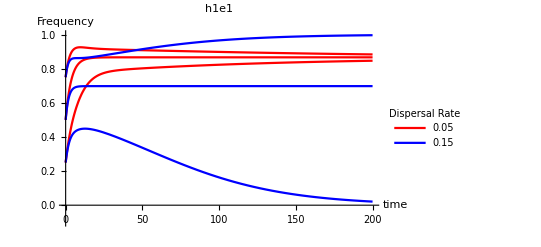

```mathematica
fxntable=Table[{{di,h0},dynsol[di,h0,s0]},{di,{0.05,0.15}},{h0,{0.25,0.5,0.75}},{s0,{0.5}}];
fxntable2=Flatten[fxntable,2];
h1e1v=fxntable2[[All,2,1]];
h1e2v=fxntable2[[All,2,2]];
s1e1v=fxntable2[[All,2,3]];
s1e2v=fxntable2[[All,2,4]];
cols=fxntable2[[All,1]];
stratlist={"h1e1","h1e2"};
dlist={0.05,0.15};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]]},{i,1,Length[linelist]}]~Flatten~1;
thisplot=Legended[Plot[{h1e1v},{t,0,200},PlotRange->{-0.1,1},PlotStyle->{Red,Red,Red,Blue,Blue,Blue},AxesLabel->{"time","Frequency"},PlotLabel-> "h1e1" ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
```

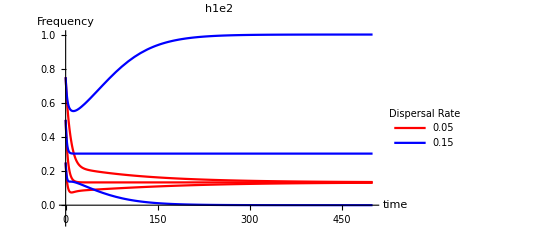

```mathematica
host2plot=Legended[Plot[{h1e2v},{t,0,500},PlotRange->{-0.1,1},PlotStyle->{Red,Red,Red,Blue,Blue,Blue},AxesLabel->{"time","Frequency"},PlotLabel-> "h1e2" ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
```

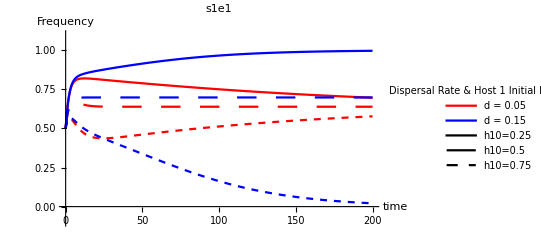

```mathematica
Legended[Plot[{s1e1v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e1" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

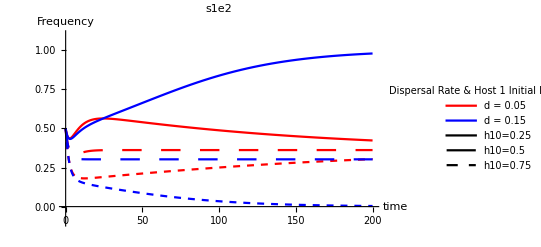

```mathematica
Legended[Plot[{s1e2v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e2" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

### Increasing the symbiont dispersal rate:

```mathematica
dynsol=ParametricNDSolveValue[dynsysdh[h0,h0,s0,s0,0.1,-0.7,0.1,-0.7,0.05,dh],{h1[t],h2[t],s1[t],s2[t]},{t,0,500},{dh,h0,s0}]
```

ParametricFunction[<>]

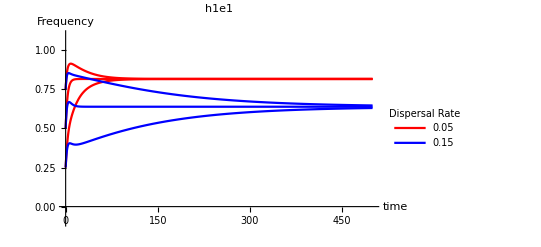

```mathematica
fxntable=Table[{{di,h0},dynsol[di,h0,s0]},{di,{0.05,0.15}},{h0,{0.25,0.5,0.75}},{s0,{0.5}}];
fxntable2=Flatten[fxntable,2];
h1e1v=fxntable2[[All,2,1]];
h1e2v=fxntable2[[All,2,2]];
s1e1v=fxntable2[[All,2,3]];
s1e2v=fxntable2[[All,2,4]];
cols=fxntable2[[All,1]];
stratlist={"h1e1","h1e2"};
dlist={0.05,0.15};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]]},{i,1,Length[linelist]}]~Flatten~1;
Legended[Plot[{h1e1v},{t,0,500},PlotRange->{-0.1,1.1},PlotStyle->{Red,Red,Red,Blue,Blue,Blue},AxesLabel->{"time","Frequency"},PlotLabel-> "h1e1" ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
```

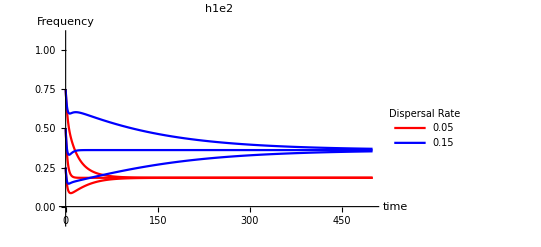

```mathematica
host2plot=Legended[Plot[{h1e2v},{t,0,500},PlotRange->{-0.1,1.1},PlotStyle->{Red,Red,Red,Blue,Blue,Blue},AxesLabel->{"time","Frequency"},PlotLabel-> "h1e2" ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
```

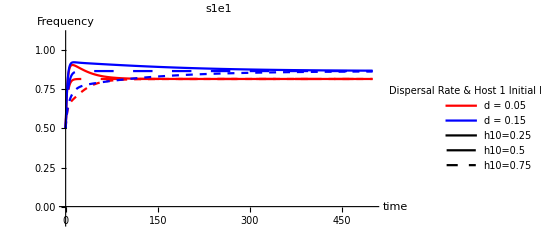

```mathematica
Legended[Plot[{s1e1v},{t,0,500},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e1" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

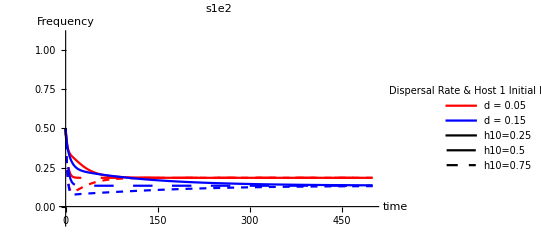

```mathematica
Legended[Plot[{s1e2v},{t,0,500},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e2" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

## Simulating many trajectories:

```mathematica
PlotWSFN[h10_,h20_,s10_,s20_,ΔHms_,ΔHgh_,ΔSmh_,ΔSgs_,ds_]:={
tmax=10000;
dynsol=ParametricNDSolveValue[dynsysdh[h10,h20,s10,s20, ΔHms,ΔHgh,ΔSmh,ΔSgs,ds,dh],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{dh,h10}];
fxntable2=Table[{dh,h10,dynsol[dh,h10]},{h10,0,1,0.01},{dh,0,0.5,0.01}]~Flatten~1;
allds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{allds,averagef,h1e1v};
h1e2p=Transpose@{allds,averagef,h1e2v};
s1e1p=Transpose@{allds,averagef,s1e1v};
s1e2p=Transpose@{allds,averagef,s1e2v};
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-0.01,0.5+0.01},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

### High Symbiont Dispersal and GXE<GXG:

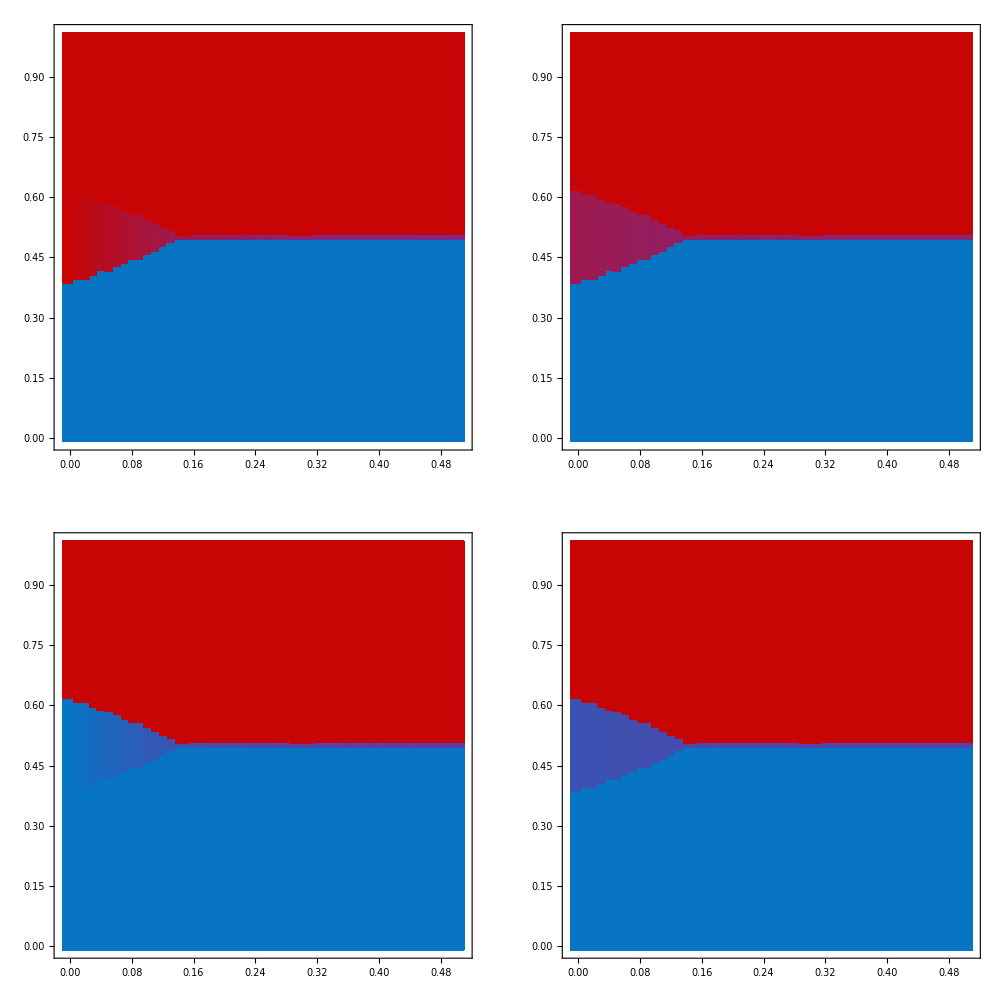
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.25]
```

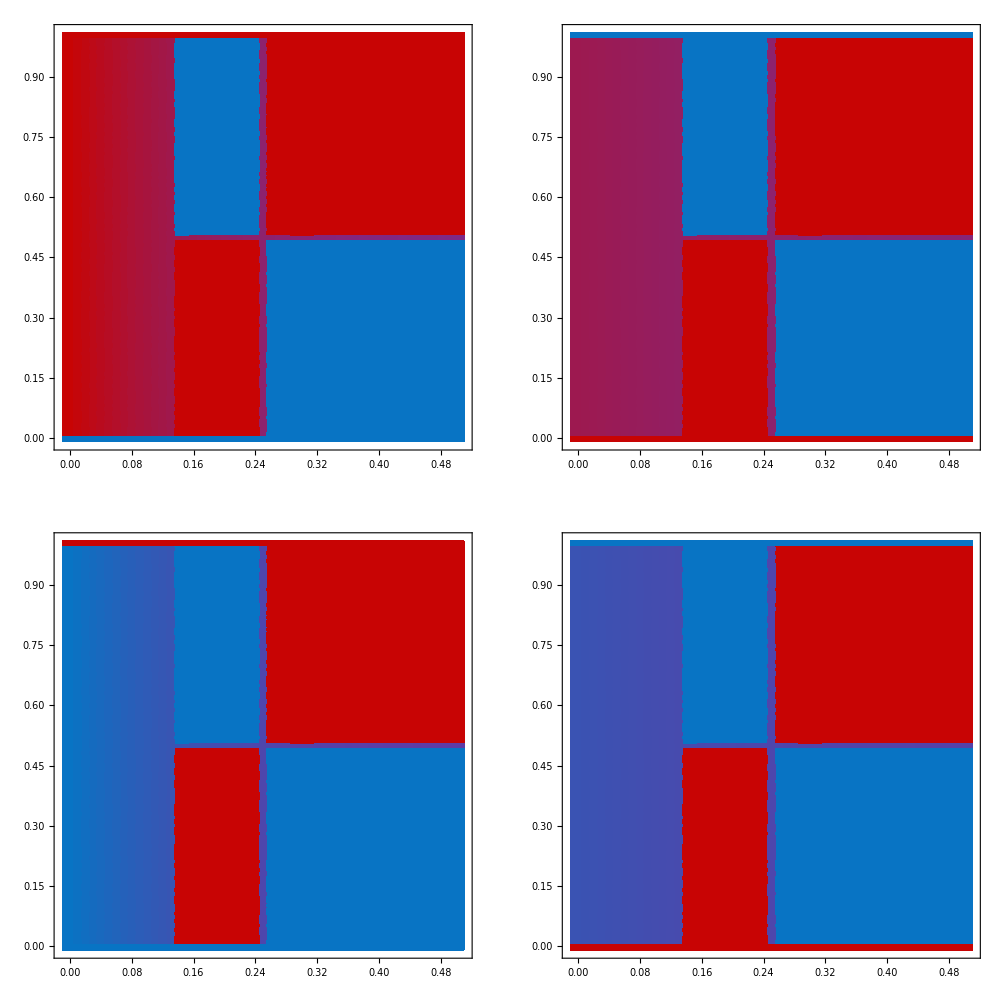
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.25]
```

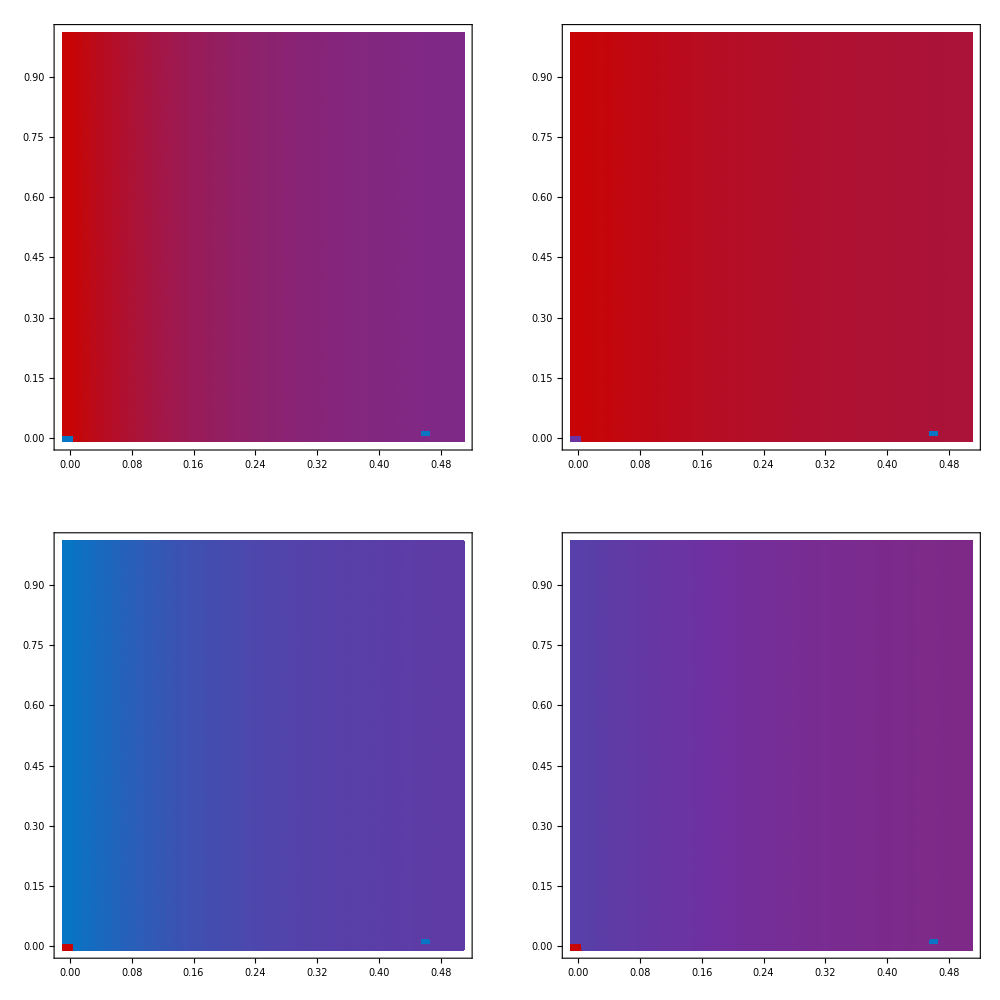
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.25]
```

### Moderate Symbiont Dispersal and GXE<GXG:

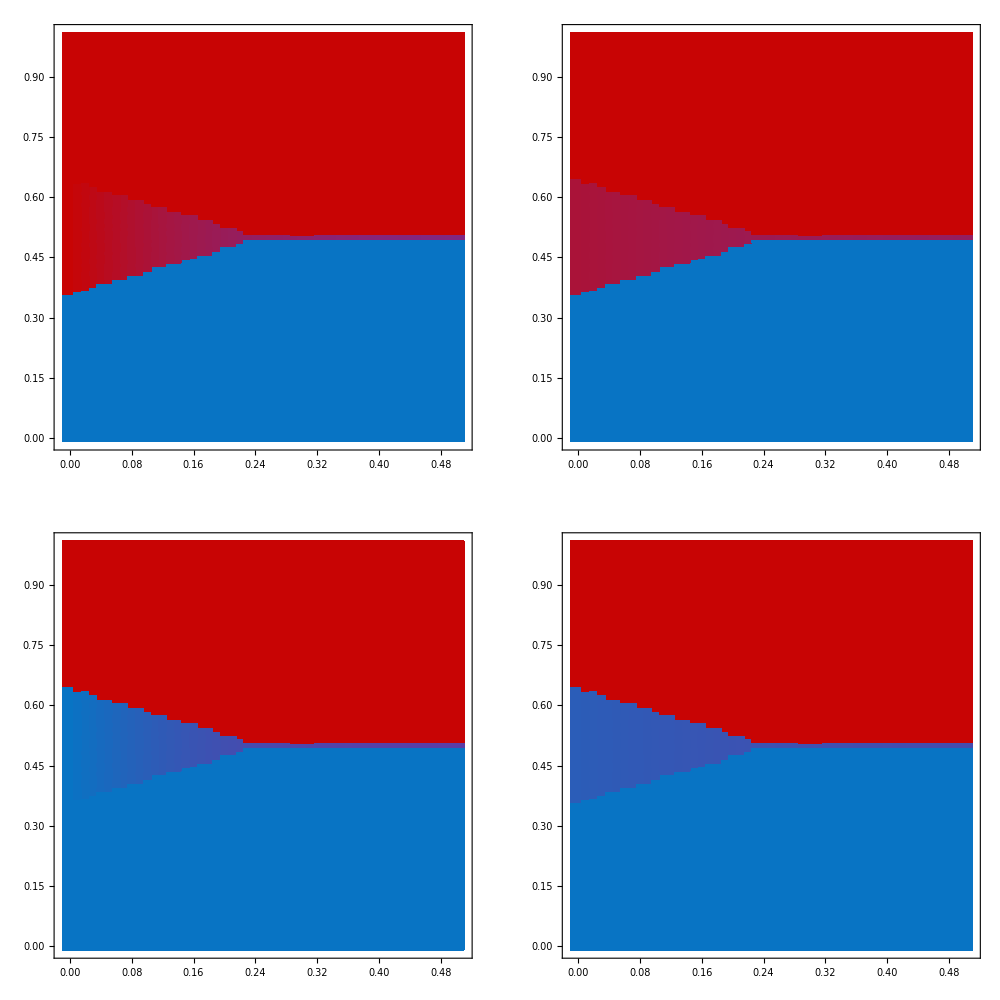
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.15]
```

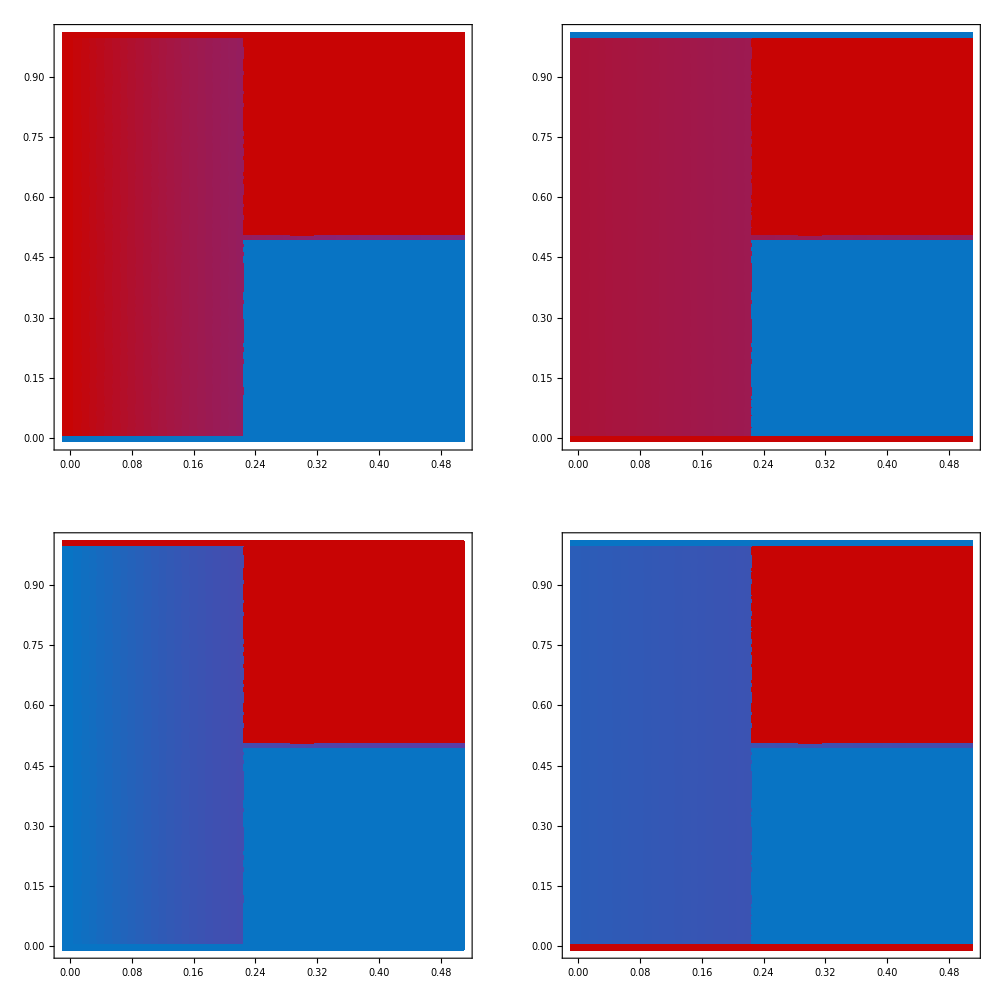
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.15]
```

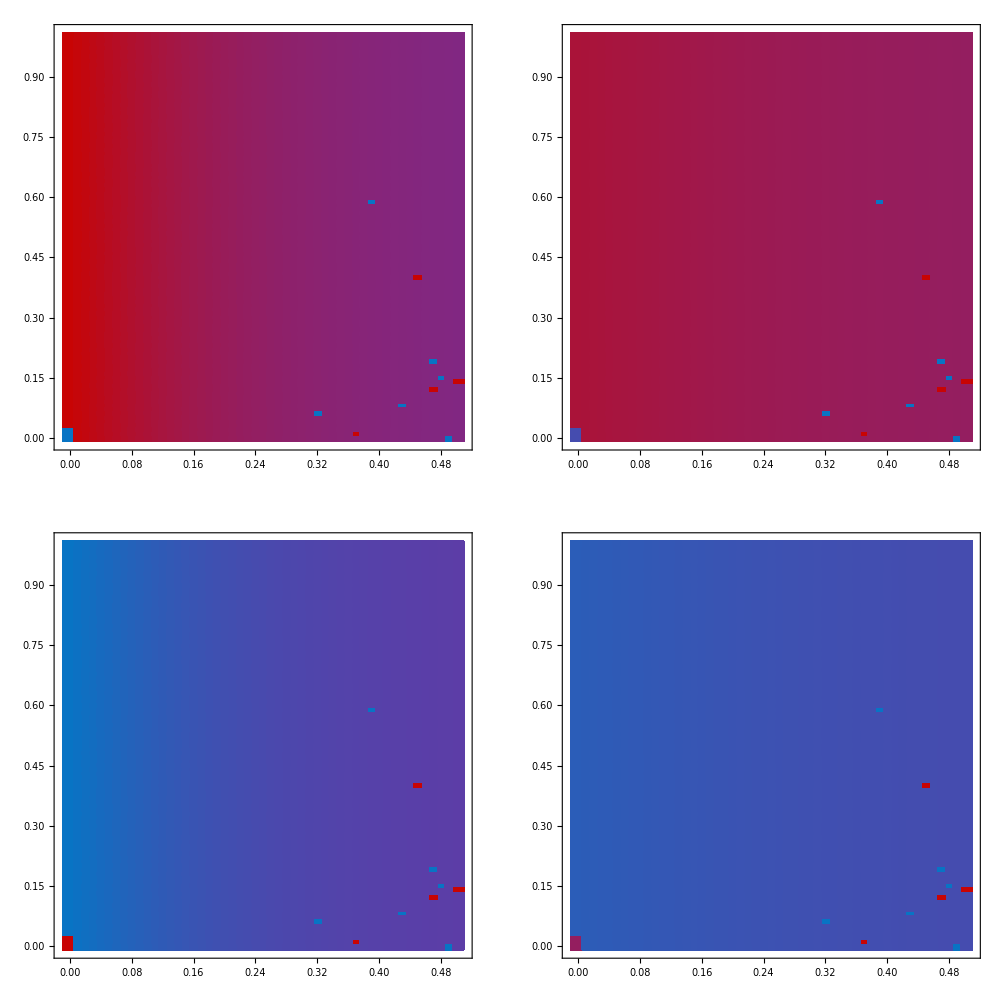
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.15]
```

### Low Symbiont Dispersal and GXE<GXG:

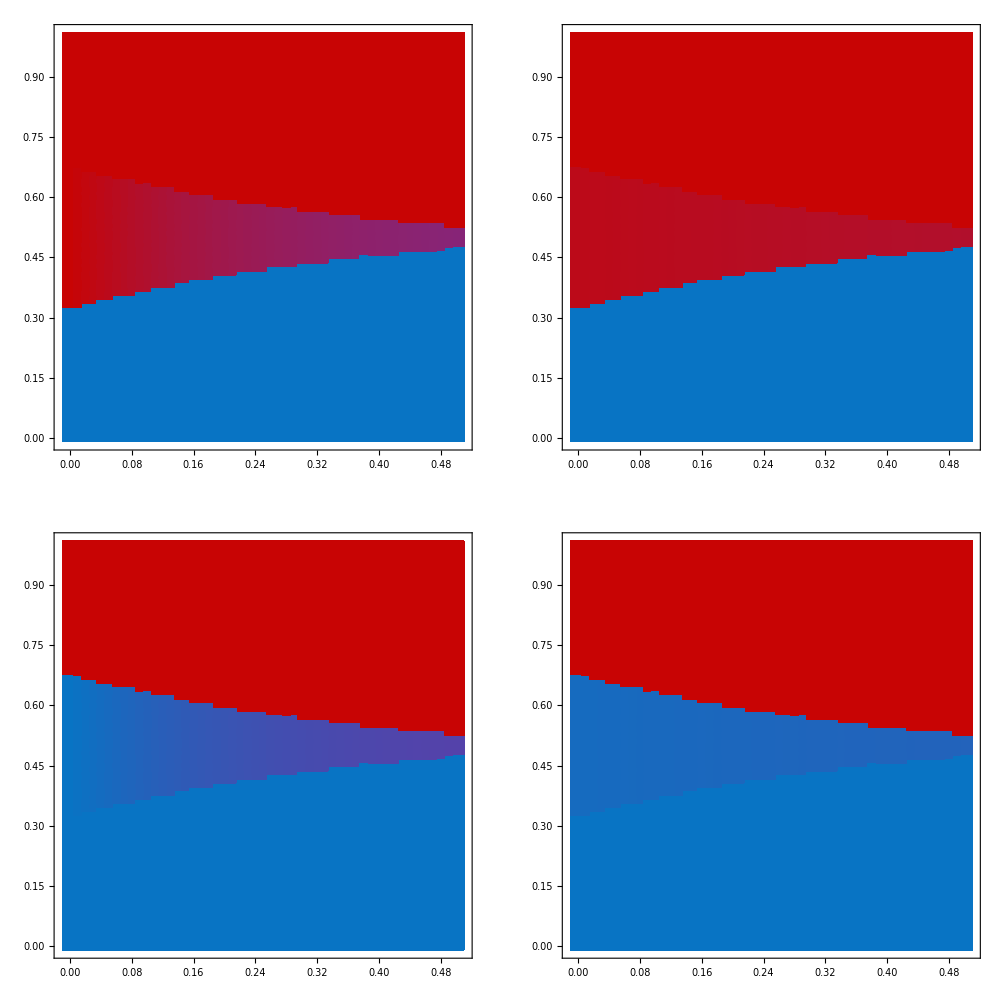
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.05]
```

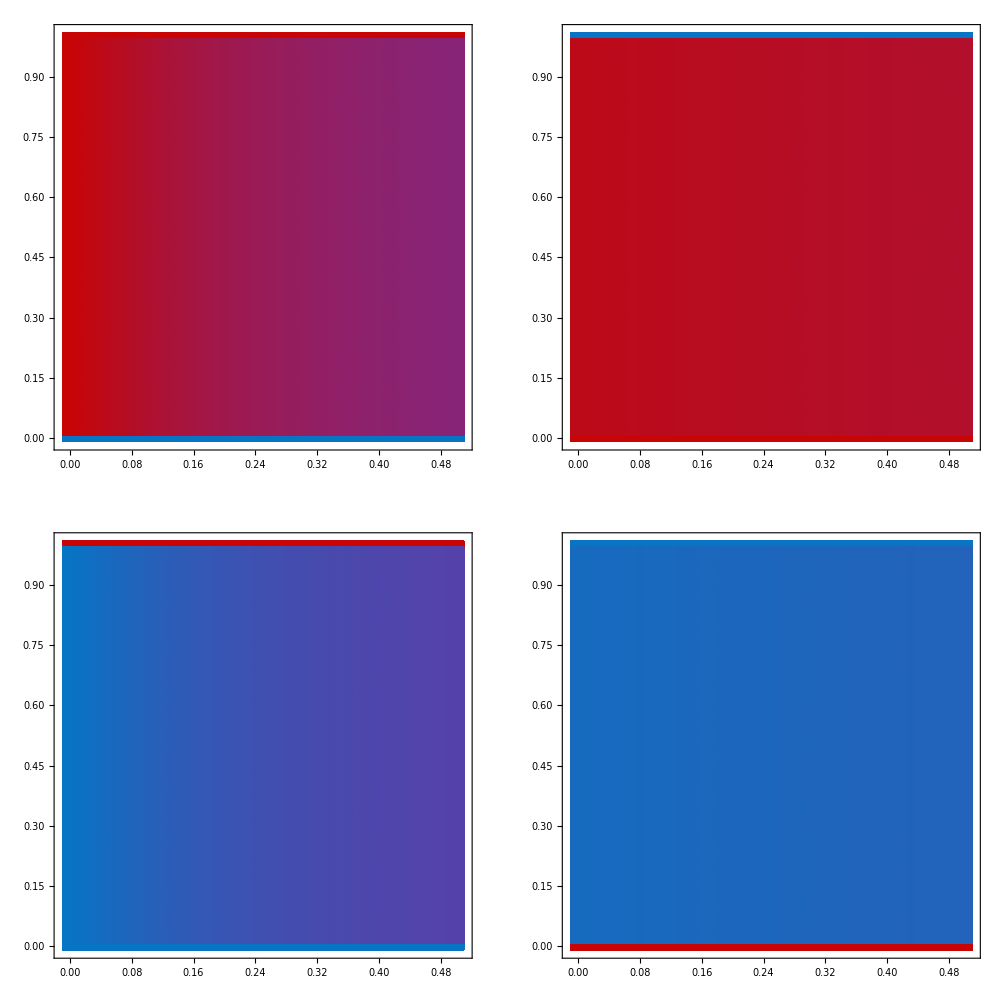
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.05]
```

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.05]
```

{-Graphics-Initial FrequencyDispersal}

### High Symbiont Dispersal and GXE>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.25]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.25]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.25]
```

{-Graphics-Initial FrequencyDispersal}

### Moderate Symbiont Dispersal and GXE>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.15]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.15]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.15]
```

{-Graphics-Initial FrequencyDispersal}

### Low Symbiont Dispersal and GXE>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.05]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.05]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.05]
```

{-Graphics-Initial FrequencyDispersal}

### High Symbiont Dispersal and GXE>>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.25]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.25]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.25]
```

{-Graphics-Initial FrequencyDispersal}

### Moderate Symbiont Dispersal and GXE>>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.15]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.15]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.15]
```

{-Graphics-Initial FrequencyDispersal}

### Low Symbiont Dispersal and GXE>>GXG:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.05]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.05]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.05]
```

{-Graphics-Initial FrequencyDispersal}